# The New Seeker

Brian Beckman
28 Aug 2019

Find a 2,000-dimensional needle in a 2,000-dimensional haystack 
more than 80% of the time in fewer than 160,000 sequential judgments. We once succeeded in finding a 5,000-dimensional needle in a 5,000-dimensional haystack in 1.3 million judgments; that trial took a couple of days to debug and .0cto run, so we haven’t repeated it yet.

More generally, we show a method of searching for random constant d-vector targets by Euclidean distance using nothing but binary preference judgments, which simulate human-preference learning. Human-preference learning is interesting because it is cheap at scale: a thousand judgments might cost $10. It’s also interesting because it might lead to controller policies beyond the capabilities of expert engineers.

Ordinary human judgment is actually very refined. Almost anyone can tell the difference, at-a-glance, between an elegant gymnastic performance and a merely flawless one. However, can anyone write a robotics controller that can demonstrate such distinctions? Can a reinforcement-learning engineer write a reward function that can derive elegant versus flawless gymnastics? This notebook is part of a research programme in robotics. A premise of that programme is that by appropriately harvesting judgments from ordinary, non-expert human observers, we can machine-learn robotics policies that are beyond the capabilities of expert engineers to write explicitly, even if indirectly through reward functions, and that exhibit such fine distinctions.

A limitation of the present work is that it has only been demonstrated on convex functions like Euclidean distance. We believe it will still work in scenarios where finding any one of many local maxima is acceptable, as with optimal control theory, but we have not demonstrated so in this notebook.

## Problem Statement

Estimate N, the number of judgments needed to find a local maximum of some real-valued benefit function. N comes along with a second hyperparameter, the shrinkage factor Δ, explained below. We cannot find N without specifying Δ and vice versa. N and Δ are linked in a way we do not fully understand. However, we can find good, paired values of N and Δ such that searches succeed most or even all of the time. 

The benefit function studied in this notebook is singly convex, i.e., there is only one local maximum. Real-world benefit functions may have more than one acceptable local maximum. Therefore, the estimated Ns in this notebook are conservative. Real-world judgment counts could be many fewer if searches are allowed to find any acceptable local maximum.

One of our simulated judgments 
	1. starts with two Gaussian guesses, A and B, centered at the current best estimate y_p of the target, and within a statistical search radius σ_p, the standard deviation of a Gaussian pseudo-random number generator
	2. consults an oracle for the Euclidean distance from the true target for each of A and B (in a real-world setting, the true target is not known; instead, a human will choose, subjectively, between the two, and it is precisely this subjective judgment we wish to harvest)
	3. re-centers the next search at at the closer of A and B: y_p←A if A is closer to true target, else y_p←B
	4. sets a smaller search radius for the next search (σ_p←Δ σ_p;Δ<1); this step explains why Δ is the “shrinkage factor”

A trial is a sequence of judgments. 2,000 dimensions with a maximum "gas-tank" of 160,000 judgments is the biggest trial in this notebook. It can take a couple of minutes to run on one core. We call the maximum number of judgments, say 160,000, a gas tank, because we fail a search when it "runs out of gas," that is, takes more judgment time than we are willing to wait. We express how long we're willing to wait by putting a number like 160,000 in the gas tank. In another place, we ran a C++ version of this code, and found a 5,000 D needle in a 5,000 D haystack in 1.3 million out of a gas tank of 100 million judgments. That was the single, biggest trial we’ve run so far with any software. It entailed a lucky guess at the correct Δ. It took about three hours to run on one core. We do not yet know whether Mathematica can do a trial that big. 

There is a secondary, software-engineering story about C++ versus Mathematica, covered in another tech report.

In this notebook, we do episodes of 1600 trials in 16 rollouts of 100 trials each. Each rollout tries a different shrinkage factor Δ, 16 in all. It takes Mathematica about 6 hours on six cores in 64 GB of memory for an episode of 1600 trials at 2,000 dimensions and a gas tank of 160,000. That's about a quarter billion 2000-vectors, or half a trillion Gaussian samples.

### Definitions

```mathematica
({{Style["Term",Bold,Italic], Style["synonym",Bold,Italic], Style["description",Bold,Italic]}, {"Episode", "rollouts", "parallelizable bunch of rollouts"}, {"Rollout", "trials", "parallelizable bunch of trials"}, {"Trial", "trajectory, trip", "non-parallelizable sequence of judgments"}, {"Judgment", "", "choice of one of two guesses, A and B"}, {"Guess", "", "a d-vector"}})//TableForm
```

Term | synonym | description
Episode | rollouts | parallelizable bunch of rollouts
Rollout | trials | parallelizable bunch of trials
Trial | trajectory, trip | non-parallelizable sequence of judgments
Judgment |  | choice of one of two guesses, A and B
Guess |  | a d-vector

## Searching for Shrinkage

We sweep the the shrinkage factor Δ in an episode, one Δ in each of 16 rollouts, looking for the best Δ for a given dim and maxIter, the size of the gas tank. For the biggest episode in this notebook, with d=2000 and gas tank=maxIter=160000, the best Δ is 0.999919.

### Number of Leading Nines in Δ

ΔFromLd and its inverse, ldFromΔ, convert back and forth between Δ and its number of leading nines.

```mathematica
ClearAll[ldFromΔ,ΔFromLd];
ldFromΔ[Δ_]:=-Log10[1.-Δ];
ΔFromLd[lm_]:=1.-10.^-lm;
Table[{ld,NumberForm[ΔFromLd[ld],17]},{ld,1,7,1}]//Grid
```

1 | 0.9
2 | 0.99
3 | 0.999
4 | 0.9999
5 | 0.99999
6 | 0.999999
7 | 0.9999999

## How a Trial Dies or Wanders

### Dying: Δ too Small

The rate of decrease of the search radius is proportional to 1-Δ. The rate gets larger as Δ get smaller. When Δ is too small, the search radius decreases too quickly The trial will run out of gas before it gets close to the target. We can guess, ahead of time, that it will run out of gas, and we can cut off the trial early, before we actually do run out of gas ("We're going in the right direction, but we don’t have enough gas.”). The point of quitting early is to save wall-clock time. These episodes take many hours to run and anything that speeds them up without ruining their results is worth the trouble. 

We predict running out of gas when the distance dist of y_p from the true target is greater than 10×maxIter×σ_p; we guess that we're probably not going to get there in 10×maxIter more tries even if we weren't shrinking σ_p every step; we don't have enough gas by an order of magnitude. We call such a trial "dead." This particular death prediction formula 10×maxIter×σ_p is just a heuristic. We might find a better heuristic with harder theoretical thinking. However, we have a way to find out whether this heuristic is too aggressive, i.e., kills the trial too early: run some trials with the death-predictor off and compare them to trials in the same number of dimensions with the predictor on. If our heuristic is not too aggressive, then the convergence rates with the predictor on or off should be about the same. If the heuristic is too aggressive, then the convergence rate will be higher with the predictor off. We call this test process "assessing the death tax" in a section below.

### Wandering: Δ too Big

When Δ is too big, we never find the target because our search radius is always too big; it doesn't shrink the search radius σ quickly enough. Such trials are "wandering." We can't find out about wandering trials till they actually run out of gas.

## Algorithm

This algorithm was discovered after two previous attempts. Both attempts produced correct algorithms, but they did not perform well in certain ways described below.

Given dimension d≥2, shrinkage factor Δ<1, tolerance tol=0.01, current iteration number i, current distance dist from target, and "gas tank" maxIter≥1, choose a target d-vector uniformly in the d-ball.

Set y_p←{0}_(ℝ^d), the zero vector in d dimensions; σ_p←1, implying that the covariance matrix is the Identity matrix in d dimensions, 𝟙_(ℝ^d); and dist←0.

Reaping the values that are sown in step 10:

Catching the values potentially thrown in steps 5, 6, 7.3, and 8.3:

Do the death and wandering tests early to avoid computing new samples when not necessary.

if dist>10×maxIter×σ_p, throw {y_p,dist,σ_p,target,Δ,i}, "Dead."

If i≥maxIter, throw {y_p,dist,σ_p,target,Δ,i}, “Wandering.”

Generate and test the two points sequentially to avoid computing B if A is close enough.

Generate and Test A

Generate guess A normally distributed around center y_p with standard deviation σ_p.

Calculate Euclidean distance d_A=||y_p-A(||)_(L_2^d)

If d_A<tol throw {A,d_A,σ_p,target,Δ,i}, “Found.”

Generate and Test B

Generate guess B normally distributed around center y_p with standard deviation σ_p.

Calculate Euclidean distance d_B=||y_p-B(||)_(L_2^d)

If d_B<tol throw {B,d_B,σ_p,target,Δ,i}, “Found.”

Prepare iteration;

If d_A<d_B, set y_p←A and dist←d_A, else set y_p←B and dist←d_B.

Set σ_p←Δ σ_p, i←i+1

Optionally, Sow {y_p,dist,σ_p} where it can be Reaped by the caller

Go to 3

Iterate steps 3→11 with a fast, functional fold. Fold goes by the Python name reduce or by the C# name Aggregate. Fold revises estimates by internally iterating over updates. Fold is a function of three arguments: the first argument is a binary function that converts a state and an update into a new state, the second argument is an initial state value, and the third argument is a stream or sequence of updates.

Fold(binaryFunction, initialState, sequenceOfUpdates) = do {state←binaryFunction(state, update)} for every update in updates.

In our particular case, we are folding over the binary function seek, whose two inputs are each tuples:

Fold(seek,initialState:{y_p={0}_(ℝ^d),dist=0,σ=1},updates:Table[{Δ,target,tol,maxIter,i} for i in Range[{1,maxIter}]]), 
=do{{y_p,dist,σ_p}←seek(state:{y_p,dist,σ_p},update:{Δ,target,tol,maxIter,i})} for i from 1 to maxIter.

This form iteratively replaces the tuple containing the current state estimate with a new tuple, driven by the update tuple, which contains constants {Δ,target,tol,maxIter} and one variable, i. We put the constants in the update tuple to avoid pulling them from the global environment; that choice may be costly because we make so many copies.

## Sampling

### Uniformly in the d-Ball

This algorithm exploits Archimedes’s “hat-box” theorem and is the fastest known (see Ops Robotics Tech Report 018). By default, it generates 50,000 uniformly random vectors in 2 dimensions, but it works in any number of dimensions greater than or equal to 2.

```mathematica
ClearAll[uniformInBall];
uniformInDball[n_:50000,d_:2]:=
Drop[#,2]&/@
Normalize/@
RandomVariate[
NormalDistribution[],{n,d+2}];
```

There follows a visual demonstration of uniformity.

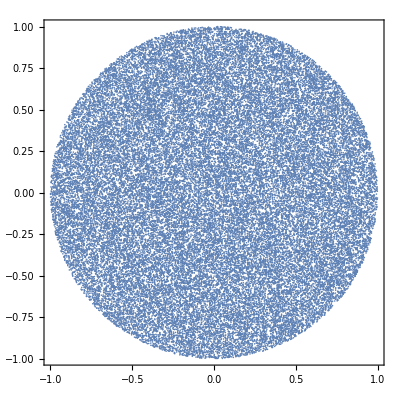

```mathematica
ListPlot[uniformInDball[],AspectRatio->Automatic,Frame->True]
```

There follows a function for generating a single, uniform, random d-vector for a target.

```mathematica
ClearAll[getTarget];
getTarget[d_:4]:=uniformInDball[1,d]⟦1⟧;
```

## Seeking

## Bisecting for the Decay

For each dim, tol, maxIter; find, via bisection, the smallest decay Δ that converges the most rollouts in an episode, i.e., in the smallest number of judgments on the average. Bisection is “divide-and-conquer” search and runs in logarithmic time. However, we must bisect on both Δ and maxIter simultaneously. Our software does not automatically do that, so we bisect manually for now (TODO), guessing at Δ and maxIter, then refining the guesses based on output.

### Do One Judgment

The following function, doJudgment, performs one judgment. It throws when it dies, wins, or runs out of gas wandering, so the caller handles all returns in Catch blocks. It decays standard deviation σ rather than covariance, σ^2. Some other versions of seeker decay the covariance instead. Be aware of this point when comparing different studies of seeker.

Call doJudgment from Fold wrapped in three nested Catches, one for each of “Found,” “Dead,” and “Wandering.” Optionally, doJudgment reap intermediate results for visualization, logging, debugging by setting sow (lower case) to Sow. Sow uses memory, so set sow to Identity for big runs. Likewise, deathTest defaults to True; set it temporarily (in Block) to False for the purpose of determining the “death tax.” If the death test is too aggressive, you will get more convergence with deathTest set to False, that is, you will “feel” the “death tax.”

The parameters of doJudgment are split into two lists, the left list holding the prior state, the right holding inputs for the current call. The output is a new state, so doJudgment meets the requirements for Fold.

```mathematica
sow=Sow;
deathTest=True;
ClearAll[doJudgment];
doJudgment[{yp_,dist_,σ_},{Δ_,tar_,tol_,maxIter_,i_}]:=
With[{},
If[(deathTest && (dist>10maxIter σ)),Throw[{yp,dist,σ,tar,Δ,i},"Dead"]];
If[i≥maxIter,Throw[{yp,dist,σ,tar,Δ,i},"Wandering"]]; 
With[{a=Map[RandomVariate[NormalDistribution[#,σ]]&,yp]},
With[{da=EuclideanDistance[tar,a]},
If[da<tol,Throw[{a,da,σ,tar,Δ,i},"Found"]];
With[{b=Map[RandomVariate[NormalDistribution[#,σ]]&,yp]},
With[{db=EuclideanDistance[tar,b]},
If[db<tol,Throw[{b,db,σ,tar,Δ,i},"Found"]];
With[{νσ=Quiet[σ*Δ]},
sow@If[da<db,{a,da,νσ},{b,db,νσ}]]]]]]];
```

### Convenient Form for Output

The following converts outputs from machine-convenient, position-sensitive list form to human-convenient Association form (like dictionary in Python).

```mathematica
ClearAll[trialDict];
trialDict[{yp_,dist_,σ_,tar_,Δ_,i_},tag_]:=
<|"yp"->yp,"dist"->dist,"σ"->σ,"tar"->tar,"Δ"->Δ,"i"->i,"tag"->tag|>;
```

### Timing Test

With constants in the update, we don’t need global variables and the code is cleaner. However, it might be expensive to copy constants just for convenience. The following shows that the difference in timing is NOT significant.

#### Copying Constants into Every Update

The With expression introduces constants into its scope.

```mathematica
With[{result=
AbsoluteTiming[
Block[{sow=Identity,dim=200},
With[{tar=getTarget[dim],tol=0.01,maxIter=20000},
Reap[Catch[Catch[Catch[Fold[
doJudgment,{ConstantArray[0,dim],0,1},
Table[{0.9993,tar,tol,maxIter,i},{i,maxIter}]],
"Found",trialDict],"Dead",trialDict],"Wandering",trialDict]]]]]},
{result[[1]],result[[2,1]]["tag"],result[[2,1]]["i"]}]
```

{1.21804,Found,14562}

#### Setting Constants Globally

Δ, tar (target), tol (tolerance), maxIter are now global variables; set them directly or in a Block expression.

```mathematica
ClearAll[Δ,tar,tol,maxIter,doJudgmentFromGlobals];
doJudgmentFromGlobals[{yp_,dist_,σ_},i_]:=
CompoundExpression[
If[(deathTest && (dist>10maxIter σ)),Throw[{yp,dist,σ,tar,Δ,i},"Dead"]],
If[i≥maxIter,Throw[{yp,dist,σ,tar,Δ,i},"Wandering"]],
With[{a=Map[RandomVariate[NormalDistribution[#,σ]]&,yp]},
With[{da=EuclideanDistance[tar,a]},
If[da<tol,Throw[{a,da,σ,tar,Δ,i},"Found"]];
With[{b=Map[RandomVariate[NormalDistribution[#,σ]]&,yp]},
With[{db=EuclideanDistance[tar,b]},
If[db<tol,Throw[{b,db,σ,tar,Δ,i},"Found"]];
With[{νσ=Quiet[σ*Δ]},
sow@If[da<db,{a,da,νσ},{b,db,νσ}]]]]]]];
With[{result=
AbsoluteTiming[
Block[{sow=Identity,dim=200,Δ=0.9993,tol=0.01,maxIter=20000,
tar=getTarget[200],$IterationLimit=20,$RecursionLimit=20},
Reap[Catch[Catch[Catch[Fold[
doJudgmentFromGlobals,{ConstantArray[0,dim],0,1},Range[maxIter]],
"Found",trialDict],"Dead",trialDict],"Wandering",trialDict]]]]},
{result[[1]],result[[2,1]]["tag"],result[[2,1]]["i"]}]
```

{1.19329,Found,14491}

## Visualization Gadget

With the following visualization, you can experiment interactively with the hyperparameters. Try the various sliders and dimension buttons. Δ is represented by, ld, its number of leading nines; tol and gas tank (number of reps aka maxIter) are logarithmic. 

The defaults are set at a soft test, dim=2, Δ=0.9, number of reps=100; -2, 1, 2, 2, 2 for the controls from top to bottom. This draws quickly enough that you can pound the DO AGAIN button repeatedly. 

A harder test is dim=200, Δ=0.999483, number of reps=100000; -2, 3.25, 5, 2, 200 for the controls from top to bottom. It might take a minute or two to draw the picture. It succeeds most of the time after about 17500 judgments. Be patient. If you get $Aborted, press the DO AGAIN button and wait a little. 

Intermediate dimensions, 5, 10, 20, 50, 100, respond more quickly. Any larger dimensions and you may run out of patience. We have not tested this visualization gadget much harder than dim=200.

```mathematica
ClearAll[vizSeek2D002,dist,yp,σ,cov,i];
picker[n_]:=#⟦n⟧&;{yp,dist,σ}=picker/@Range[3];
echo=Echo;
DBALLRADIUS=1.0;
vizSeek2D002[tol_:0.1,Δ_:0.99599,maxIter_:10000,pr_:10,dim_:2]:=
(* For picking a random pair of dims for display from big-dim vectors. *)
With[{indices=Sort@RandomSample[Range[dim],2]},
With[{indexer={#⟦indices⟦1⟧⟧,#⟦indices⟦2⟧⟧}&},
With[{sampler={indexer[yp[#]],dist[#],σ[#]}&},
With[{tar=getTarget[dim],ini=ConstantArray[0,dim]},
With[{result=Reap[Catch[Catch[Catch[Fold[
doJudgment,{ini,0,DBALLRADIUS},(* algo step 2 *)
Table[{Δ,tar,tol,maxIter,i},{i,maxIter}]],
"Found",trialDict],"Dead",trialDict],"Wandering",trialDict]]},
With[{tag=result⟦1⟧["tag"],points=result⟦2,1⟧,smtar=indexer@tar,sampled=sampler/@result⟦2,1⟧,l=Length[result⟦2,1⟧]},
Show[Graphics[{
LightGray,Disk[],White,Disk[smtar,0.3],Black,Circle[smtar,0.3],
MapIndexed[
{Hue[(2.+#2*4/l)/6.],Circle[yp[#1],σ[#1]],Point[yp[#1]]}&,
sampled],
Text[Style[{l,tag(*,Δ,tol*),σ[Last[sampled]]},"Text",Background->White],{0,pr*0.960}]
}],AspectRatio->Automatic,Frame->True,PlotRange->1.025*pr]]]]]]];
Manipulate[
vizSeek2D002[10.^le,1.-10^-ld,Floor[10.^lm],r,dim],
Row[{Button["  DO AGAIN  ",(le++;le--)&],"    ",
Button["  RESET  ",(le=-2;ld=1.0;lm=2;r=2;dim=2)&]}],
{{le,-2,"log_10(tol)"},-5,0,0.1,Appearance->{"Open","Labeled"}},
{{ld,1.0,"-log_10(1-Δ)"},0.,5.,0.25,Appearance->{"Open","Labeled"}},
{{lm,3,"log_10(reps)"},0,7,1,Appearance->{"Open","Labeled"}},
{{r,2,"plot range"},1,30,1,Appearance->{"Open","Labeled"}},
{{dim,2},{2,5,10,20,50,100,200,500,1000,2000,5000,10000},ControlType->Setter}]
```

Here is an interactive gadget that does not Sow. It runs much more quickly than the visualization and confirms the visualization. We did not change the call to Reap so as to avoid the risk of breaking code.

```mathematica
ClearAll[printSeek2D002];
printSeek2D002[tol_:0.1,Δ_:0.99599,maxIter_:10000,pr_:10,dim_:2]:=
Block[{sow=Identity},
(* For picking a random pair of dims for display from big-dim vectors. *)
With[{indices=Sort@RandomSample[Range[dim],2]},
With[{indexer={#⟦indices⟦1⟧⟧,#⟦indices⟦2⟧⟧}&},
With[{sampler={indexer[yp[#]],dist[#],σ[#]}&},
With[{tar=getTarget[dim],ini=ConstantArray[0,dim]},
With[{result=Reap[Catch[Catch[Catch[Fold[
doJudgment,{ini,0,DBALLRADIUS},
Table[{Δ,tar,tol,maxIter,i},{i,maxIter}]],
"Found",trialDict],"Dead",trialDict],"Wandering",trialDict]]},
<|"σ"->result⟦1⟧["σ"],"i"->result⟦1⟧["i"],"tag"->result⟦1⟧["tag"],"Δ"->Δ,"dim"->dim,"tol"->tol|>]]]]]];
Manipulate[
printSeek2D002[10.^le,1.-10^-ld,Floor[10.^lm],r,dim],
Row[{Button["  DO AGAIN  ",(le++;le--)&],"    ",
Button["  RESET  ",(le=-2;ld=1.0;lm=2;r=2;dim=2)&]}],
{{le,-2,"log_10(tol)"},-5,0,0.1,Appearance->{"Open","Labeled"}},
{{ld,1.0,"-log_10(1-Δ)"},0.,5.,0.25,Appearance->{"Open","Labeled"}},
{{lm,3,"log_10(reps)"},0,7,1,Appearance->{"Open","Labeled"}},
{{dim,2},{2,5,10,20,50,100,200,500,1000,2000,5000,10000},ControlType->Setter}]
```

## Assessing the Death Tax

### Trial

Here is a trial function that does not Sow.

```mathematica
Block[{sow=Identity},
ClearAll[trial];
trial[Δ_,tar_,tol_,maxIter_]:=
Catch[Catch[Catch[
Fold[doJudgment,
{ConstantArray[0.,Length@tar],0.,1.},
Table[{Δ,tar,tol,maxIter,i},{i,maxIter}]],
"Found",trialDict],"Dead",trialDict],"Wandering",trialDict]];
trial[.99599,getTarget[2],0.01,1000]
```

<|yp→{0.538483,0.343254},dist→0.00359788,σ→0.0363377,tar→{0.535777,0.345625},Δ→0.99599,i→826,tag→Found|>

### Fast Incremental Statistics

The following are fast incremental statistics in constant memory. See http://vixra.org/abs/1606.0328. We need them to assess success rates and thus the “death tax.”

```mathematica
ClearAll[cume,zeroStats];
zeroStats=<|"mean"->0,"min"->Infinity,"max"->-Infinity,"var"->0,"n"->0,"stddev"->0|>;
cume[runningStats_,z_]:=
With[{
m=runningStats["mean"],
max=runningStats["max"],
min=runningStats["min"],
n=runningStats["n"],
var=runningStats["var"]},
With[{K=1./(n+1.),r=z-m},
With[{var2=((n-1)var+K n r^2)/Max[1,n]},
<|"mean"->m+K r,"n"->n+1,"min"->Min[z,min],
"max"->Max[z,max],"var"->var2,"stddev"->Sqrt[var2]|>]]];
(*FoldList[cume,zeroStats,{55,89,144}]*)
```

A bunch of rollouts is an episode; doEpisode, depends on trial defined above. It introduces another hyperparameter, maxRol, the number of rollouts in an episode. In this notebook, we leave it at 100. 

There is a sample call for Δ=0.925, dim=2, gas tank=1000, that usually delivers about 85 percent success rate with deathTest=True, the default. We must do the rollouts sequentially, rather than in parallel, so we can accumulate statistics. A parallel version of statistics gathering is planned (TODO), but not necessary or even usable (impossibility explained below) for the main task of this work, finding Δ, but it would be helpful for assessing the death tax. We might replace the tail-recursive For loop with an outer Fold, but that’s yak-shaving.

### Do Episode

#### Quick Test

```mathematica
ClearAll[doEpisode];
doEpisode[Δ_,maxRol_,tar_,tol_,maxIter_]:=
Module[{irol,stats=<|"Found"->zeroStats,"Dead"->zeroStats,"Wandering"->zeroStats|>},
For[irol=1,irol≤maxRol,irol++,
With[{result=trial[Δ,tar,tol,maxIter]},
stats@result@"tag"=cume[stats@result@"tag",result@"i"]]];
Append[stats,<|"maxRol"->maxRol,"dim"->Length@tar,"tol"->tol,"Δ"->Δ,"ld"->ldFromΔ@Δ,"maxIter"->maxIter|>]];
doEpisode[0.925,100,getTarget[2],0.01,1000]
```

<|Found→<|mean→59.9881,n→84,min→21,max→122,var→270.59,stddev→16.4496|>,Dead→<|mean→146.312,n→16,min→117,max→176,var→391.963,stddev→19.798|>,Wandering→<|mean→0,min→∞,max→-∞,var→0,n→0,stddev→0|>,maxRol→100,dim→2,tol→0.01,Δ→0.925,ld→1.12494,maxIter→1000|>

We now do a fast assessment in two dimensions. Looks like, with the death test off, we don’t get a higher “Found” rate. As expected, we get no dead searches; all failures are wanderers.

```mathematica
Block[{deathTest=False},
doEpisode[0.925,100,getTarget[2],0.01,1000]]
```

<|Found→<|mean→59.0633,n→79,min→26,max→105,var→194.06,stddev→13.9305|>,Dead→<|mean→0,min→∞,max→-∞,var→0,n→0,stddev→0|>,Wandering→<|mean→1000.,n→21,min→1000,max→1000,var→0.,stddev→0.|>,maxRol→100,dim→2,tol→0.01,Δ→0.925,ld→1.12494,maxIter→1000|>

#### Slow Test

Let' s do a deeper test. This takes a few minutes to run, so we don’t want to do it too often. I commented out the input call so that it doesn’t get accidentally evaluated when we re-evaluate the entire notebook, costing us minutes of wait time. With death test on, we get 29 found and 71 dead, each after about 20000 judgments. There is plenty of benefit to the death test because it saves us about 80000 judgments for each failing trial.

```mathematica
(*doEpisode[ΔFromLd[3.+1./16.],100,getTarget@200,0.01,100000]*)
```

With death test off, we get nine more successes, but every failure is a wanderer that must be followed to the bitter end. This takes almost five times longer to run than the prior test. We deem that the death tax is measurable, but probably worth it to save some time. We will miss some searches that will eventually succeed, but not enough to make it worth waiting five or more times longer. The input call is commented out, as above, to prevent time-consuming accidental evaluations.

```mathematica
(*Block[{deathTest=False},
doEpisode[ΔFromLd[3+1/16],100,getTarget@200,0.01,100000]]*)
```

## Here’s the Beef

Sweep takes a left ld (number of nines in Δ), a right ld, a number nδld of lds to sweep, a maxRol, target, tolerance, and gas tank (maxIter). It does nδld episodes in parallel, one for each Δ implied by the left and right bounds. On my six-core laptop, it definitely runs six times faster than without the parallelism. Running this sweep in parallel also explains why we can’t run rollouts in parallel: Mathematica disllows nested parallelism.

```mathematica
ClearAll[pctFound,pctDead,pctWandering,pctFailed,costOfFinding,nJudgments];

nJudgments[episode_]:=episode["Found"]["n"]+episode["Dead"]["n"]+episode["Wandering"]["n"];
pctFound[episode_]:=((100.0 episode["Found"]["n"])/nJudgments[episode]);
pctDead[episode_]:=((100.0episode["Dead"]["n"])/nJudgments[episode]);
pctWandering[episode_]:=((100.0episode["Wandering"]["n"])/nJudgments[episode]);
pctFailed[episode_]:=(100.0(episode["Dead"]["n"]+episode["Wandering"]["n"])/nJudgments[episode]);
costOfFinding[episode_]:=episode["Found"]["mean"];

ClearAll[sweep];
sweep[lld_,rld_,nδld_,maxRol_,tar_,tol_,maxIter_]:=
ParallelMap[
echo@doEpisode[ΔFromLd@#,maxRol,tar,tol,maxIter]&,
Range[lld,rld,(rld-lld)/nδld],
Method->"FinestGrained"];
```

## Getting Ready: 20 Dimensions

Collect results in a chart. The following runs quickly enough to leave open in case of evaluation of the entire notebook.

It shows that for maxIter=1000 in 20 dimensions. The best Δ is around 0.9915. There is a bit of structure to the chart that needs explaining, and we leave that to the future. As expected, when Δ is too small, runs die, and when Δ is too large, they wander.

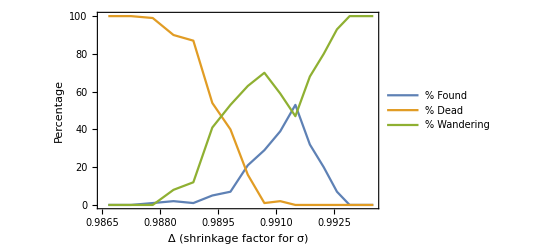

```mathematica
ClearAll[experiment];
experiment[lld_,rld_,nδld_,maxRol_,dim_,tol_,maxIter_,theEchoer_]:=
With[{data=Block[{echo=theEchoer},
sweep[lld,rld,nδld,maxRol,getTarget@dim,tol,maxIter]]},
With[{Δs=#["Δ"]&/@data},
ListLinePlot[{{Δs,pctFound/@data}ᵀ,{Δs,pctDead/@data}ᵀ,{Δs,pctWandering/@data}ᵀ},
Frame->True,
FrameLabel->{{"Percentage",""},
{"Δ (shrinkage factor for σ)",
"Seeker versus Δ, dim = "<>ToString[dim]<>", # rollouts = "<>ToString[maxRol]<>"\ntolerance = "<>ToString[tol]<>", # iters/rollout = "<>ToString[maxIter]}},
PlotLegends->{"% Found","% Dead","% Wandering"}]]];
experiment[1.875,2.1875,16,100,20,0.01,1000,Identity]
```

Spot check, on this cheap run, that the death test isn’t doing terrible harm:

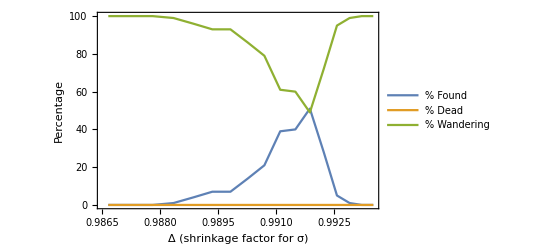

```mathematica
Block[{deathTest=False},
experiment[1.875,2.1875,16,100,20,0.01,1000,Identity]]
```

The plot has entirely different structure when the gas tank allows 4000 judgments per trial. Again, we leave investigation of such detail to later work, only mentioning it here to remind us to look into it.

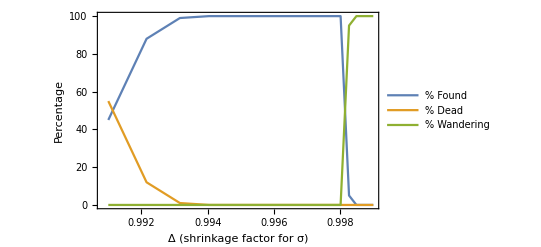

```mathematica
experiment[ldFromΔ[0.9910],ldFromΔ[0.999],16,100,20,0.01,4000,Identity]
```

## Local Stop: 200 Dimensions

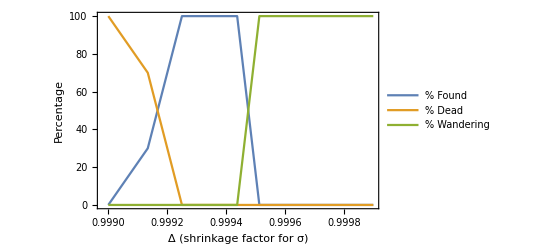

```mathematica
(*experiment[ldFromΔ@0.999,ldFromΔ@0.9999,16,100,200,0.01,20000,Identity]*)
```

## Conclusion: 2000 Dimensions

This last graph is the jewel of this notebook. It takes at least six hours to run, but shows that we can find the needle in the haystack most of the time if we set Δ and maxIter well, specifically to Δ=0.999919 and maxIter=160000, though it took several runs to find the appropriate range of Δs to sweep. It demonstrates that Mathematica, if appropriately programmed with fast and elegant functional forms, can run very challenging numerical experiments.

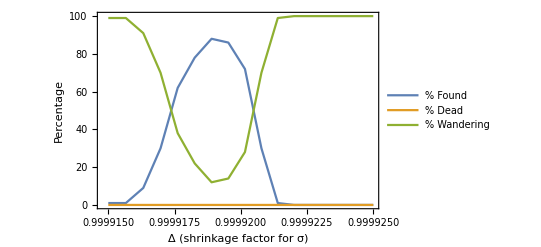

```mathematica
(*experiment[ldFromΔ@0.999915,ldFromΔ@0.999925,16,100,2000,0.01,160000,Identity]*)
```